```mathematica
f[x_]=-ⅈ Coth[ArcCoth[ⅈ x]/2];
Sq[{X_,Y_}]:=Module[{Xout,Yout,fJ,n,Ω,ω},
n=Length[Y]/2;
Ω=ArrayFlatten[({{0, IdentityMatrix[n]}, {-IdentityMatrix[n], 0}})];
ω=-Ω;
fJ=-MatrixFunction[f,-Y.ω];
Yout=fJ.Ω//FullSimplify;
Xout=Det[fJ]^(1/4)//FullSimplify;
Return[{√X Xout,Yout}]
]
Prod[{X1_,Y1_},{X2_,Y2_}]:=Module[{Mp=(Y1+Y2)/2,Mm=(Y1-Y2)/2,Y12,X12,n,Ω,ω},
n=Length[Y1]/2;
Ω=ArrayFlatten[({{0, IdentityMatrix[n]}, {-IdentityMatrix[n], 0}})];
ω=-Ω;
Y12=-1/2(Mm.Inverse[Mp].Mm+ⅈ Mm.Inverse[Mp].Ω-ⅈ Ω.Inverse[Mp].Mm+Ω.Inverse[Mp].Ω-Mp)//FullSimplify;
X12=Det[Mp]^(-1/2)//FullSimplify;
Return[{X1 X2 X12,Y12}];
]
Bures[G1_,G2_]:=Module[{},
2-2Sq[Prod[Prod[Sq[{1,G1}],{1,G2}],Sq[{1,G1}]]]⟦1⟧
]
```

```mathematica
Commuting 2 x 2 matrices:
```

```mathematica
$Assumptions={α>0,β>0};
Res=Bures[Coth[α]IdentityMatrix[2],Coth[β]IdentityMatrix[2]]
Plot3D[Sqrt[Res],{α,0.01,4},{β,0.01,4},PlotRange->All, AxesLabel->{"α","β","D^2[α, β]"}]
```

2-2 √2 √Coth[(α+β)/2] √((Coth[α/2] (Coth[α+β]-Cosh[β] Csch[α+β]))/(Coth[α/2]+Coth[β]))

-Graphics3D-

```mathematica
Non-commuting 2x 2 covariance matrices:
```

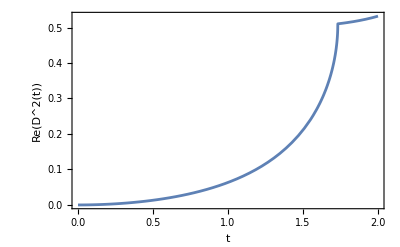

```mathematica
Plot[Bures[({{2., 0.}, {0., 2.}}),({{2., t}, {t, 2.}})]//Re,{t,0,2},PlotRange->All,Frame->True,BaseStyle->{FontFamily->"LM Roman 12",FontSize->12},FrameLabel->{"t","Re(D^2(t))"}]
```